```mathematica
λ1:= 1; 
λ2:=245*^7;
λ3:=201*^11; 
λ4:=737*^7; 
λ5:=142*^10; 
λ6:= 799*^13; 
λ7:=306*^16;
λ8:= 116*^11; 
λ9:=122*^12;
λ10:= 149*^22; 
λ11:=243*^13; 
b9b:=6406*^-4;b9a:=3594*^-4;
```

```mathematica
m[l1_,l2_,l3_,l4_,l5_,l6_,l7_,l8_,l9_,l10_,l11_,b9a_,b9b_]:= -{{l1,0,0,0,0,0,0,0,0,0,0,0},{-l1,l2,0,0,0,0,0,0,0,0,0,0},{0,-l2,l3,0,0,0,0,0,0,0,0,0},{0,0,-l3,l4,0,0,0,0,0,0,0,0},{0,0,0,-l4, l5, 0,0,0,0,0,0,0}, {0,0,0,0, -l5, l6,0,0,0,0,0,0},{0,0,0,0,0,-l6, l7,0,0,0,0,0},{0, 0, 0, 0, 0, 0, -l7, l8,0,0,0,0},{0,0,0,0,0,0,0,-l8, l9, 0, 0, 0}, {0,0,0,0,0,0,0,0,-l9*b9b, l10,0,0},{0,0,0,0,0,0,0,0,-l9*b9a,0,l11,0},{0,0,0,0,0,0,0,0,0,-l10,-l11,0}}
```

```mathematica
f := {n1[t],n2[t],n3[t],n4[t],n5[t],n6[t],n7[t],n8[t],n9[t],n10[t],n11[t],n12[t]}
```

```mathematica
LHS = m[λ1,λ2,λ3,λ4,λ5,λ6,λ7,λ8,λ9,λ10,λ11,b9a,b9b].f
```

{-n1[t],n1[t]-2450000000 n2[t],2450000000 n2[t]-20100000000000 n3[t],20100000000000 n3[t]-7370000000 n4[t],7370000000 n4[t]-1420000000000 n5[t],1420000000000 n5[t]-7990000000000000 n6[t],7990000000000000 n6[t]-3060000000000000000 n7[t],3060000000000000000 n7[t]-11600000000000 n8[t],11600000000000 n8[t]-122000000000000 n9[t],-1490000000000000000000000 n10[t]+78153200000000 n9[t],-2430000000000000 n11[t]+43846800000000 n9[t],1490000000000000000000000 n10[t]+2430000000000000 n11[t]}

```mathematica
Eqns1 = LHS[[1]]==n1'[t]
```

-n1[t]==n1'[t]

```mathematica
Eqns2 = LHS[[2]]==n2'[t]
```

n1[t]-2450000000 n2[t]==n2'[t]

```mathematica
Eqns3 = LHS[[3]]==n3'[t]
```

2450000000 n2[t]-20100000000000 n3[t]==n3'[t]

```mathematica
Eqns4 = LHS[[4]]==n4'[t]
```

20100000000000 n3[t]-7370000000 n4[t]==n4'[t]

```mathematica
Eqns5 = LHS[[5]]==n5'[t]
```

7370000000 n4[t]-1420000000000 n5[t]==n5'[t]

```mathematica
Eqns6 = LHS[[6]]==n6'[t]
```

1420000000000 n5[t]-7990000000000000 n6[t]==n6'[t]

```mathematica
Eqns7 = LHS[[7]]==n7'[t]
```

7990000000000000 n6[t]-3060000000000000000 n7[t]==n7'[t]

```mathematica
Eqns8 = LHS[[8]]==n8'[t]
```

3060000000000000000 n7[t]-11600000000000 n8[t]==n8'[t]

```mathematica
Eqns9 = LHS[[9]]==n9'[t]
```

11600000000000 n8[t]-122000000000000 n9[t]==n9'[t]

```mathematica
Eqns10 = LHS[[10]]==n10'[t]
```

-1490000000000000000000000 n10[t]+78153200000000 n9[t]==n10'[t]

```mathematica
Eqns11 = LHS[[11]]==n11'[t]
```

-2430000000000000 n11[t]+43846800000000 n9[t]==n11'[t]

```mathematica
Eqns12 = LHS[[12]]==n12'[t]
```

1490000000000000000000000 n10[t]+2430000000000000 n11[t]==n12'[t]

```mathematica
sol=NDSolve[{Eqns1,Eqns2,Eqns3,Eqns4,Eqns5,Eqns6,Eqns7,Eqns8,Eqns9,Eqns10,Eqns11,Eqns12,n1[0]==1,n2[0]==0,n3[0]==0,n4[0]==0,n5[0]==0,n6[0]==0,n7[0]==0,n8[0]==0,n9[0]==0,n10[0]==0,n11[0]==0,n12[0]==0},{n1,n2,n3,n4,n5,n6,n7,n8,n9,n10,n11,n12},{t,0,1}];
```

```mathematica
n1[0.5]
```

n1[0.5]

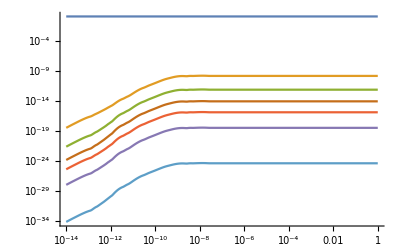

```mathematica
LogLogPlot[Evaluate[{n1[t]/n1[t],n4[t]/n1[t],n5[t]/n1[t],n6[t]/n1[t],n7[t]/n1[t],n9[t]/n1[t],n10[t]/n1[t]}/. sol],{t,1*^-14,1},PlotRange->All]
```

```mathematica
Evaluate[3*^-14*{n1[1]/n1[1],n4[1]/n1[1],n5[1]/n1[1],n6[1]/n1[1],n7[1]/n1[1],n9[1]/n1[1],n10[1]/n1[1]}/. sol]
```

{{3/100000000000000,4.07056×10^-24,2.11268×10^-26,3.75469×10^-30,9.80392×10^-33,2.45902×10^-28,1.2898×10^-38}}